# Procedural Programming

## Looping Constructs

### For

Структурата за цикъл For, има 4 задължителни комопонента: инициализация (задаване на начална стойност на брояча), проверка, инкрементиране (обновяване на стойността на брояча) и тяло. В езика Wolfram, тези 4 компонента се отделят със запетаи един от друг, като се ограждат, разбира се, в квадратни скоби.

```mathematica
list={1,2,4,5,7,8};
For[i=1,i≤Length[list],i++,
Print[list[[i]]^2]
]
```

1

4

16

25

49

64

Ако тялото на цикъла съдържа повече от една операция, всяка следваща операция се отделя от предходната с точка и запетая:

```mathematica
For[i=1,i≤Length[list],i++,
Print[i];
Print[list[[i]]^2];

]
```

1

1

2

4

3

16

4

25

5

49

6

64

N.B По подразбиране, конструкциите за цикъл (Do, For, While и др.) връщат стойност Null. Потребителят може експлицитно да укаже друга стойност, която структурата да връща, като използва Return. Обикновено, обаче, такъв тип конструкции се използват за да извършат определен брой повтарящи се операции, без да е необходимо да се връща конкретна стойност. В такива случаи, е необходимо да потиснем изхода (т.е Null), като поставим “;” след затварящата скоба на структурата. В противен случай, запазеният символ Null може да участва в последващите изчисления, което да доведе до нежелани резултати:

```mathematica
list={1,2,4,5,7,8};
listNew={0,0,0,0,0,0};
Clear[f]
f[l_]:=(
For[i=1,i≤Length[l],i++,
listNew[[i]]= (l[[i]])^2
]
Print[listNew]
)
f[list]
```

{1,4,16,25,49,64}

Null^2

Добра практика е отделните компоненти на изразите да се поставят на нов ред. Това прави кода по-лесно четим и улеснява намриането на синтактични грешки!

### While

Основните компоненти на структурата While са условие за край и тяло на цикъла, като двете се отделят със запетая.

```mathematica
a=0;
While[a>-5,
Print[a];
a--;
]
```

0

-1

-2

-3

-4

### Do

```mathematica
Do[Print[RandomInteger[10]],4]
```

3

9

7

5

```mathematica
Do[Print[k],{k,0,4}]
```

0

1

2

3

4

## Conditionals

### If

```mathematica
abs[x_]:=If[x<0,-x,x]
```

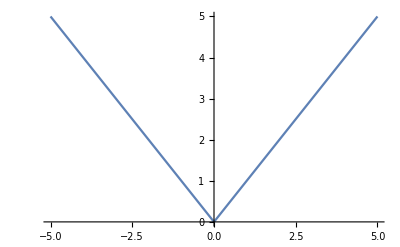

```mathematica
Plot[abs[x],{x,-5,5}]
```

### Piecewise

Piecewise е структура за създаване на по части дефинирани функции. Приема списък от наредени двойки от вида {стойност, условие за аргумента}. За повече информация, виж Help->Wolfram Documentation->Piecewise.

```mathematica
abs2[x_]:=Piecewise[{{x,x>0},{-x,x<0}}]
```

```mathematica
Plot[abs2[x],{x,-5,5}]
```

-Graphics-